```mathematica
SetOptions[EvaluationNotebook[],AutoGeneratedPackage->"DiANE.m"]
```

# DiANE - Diagram Arts and Notation of Equations

## Exports

```mathematica
FPrint::usage="";
FPrint[expr_]/;Head[$GlobalSetup]=!=Symbol:=FPrint[$GlobalSetup,expr];

FTex::usage="";
FTex[expr_]/;Head[$GlobalSetup]=!=Symbol:=FTex[$GlobalSetup,expr];

PlotDiagrams::usage="";
PlotDiagrams[expr_]/;Head[$GlobalSetup]=!=Symbol:=PlotDiagrams[$GlobalSetup,expr];
```

## Global variables

```mathematica
ModuleLoaded::dependency="The module `1` requires `2`, which has not been loaded.";

If[ModuleLoaded[FunKit]=!=True,
Message[ModuleLoaded::dependency,"DiANE","FunKit"];
Abort[];
];

If[ModuleLoaded[FEDeriK]=!=True,
Message[ModuleLoaded::dependency,"DiANE","FEDeriK"];
Abort[];
];

ModuleLoaded[DiANE]=True;
```

```mathematica
$FunKitDirectory=SelectFirst[Join[{FileNameJoin[{$UserBaseDirectory,"Applications","FunKit"}],FileNameJoin[{$BaseDirectory,"Applications","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","Applications","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","Packages","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","ExtraPackages","FunKit"}]},Select[$Path,StringContainsQ[#,"FunKit"]&]],DirectoryQ[#]&]<>"/";
```

## Pretty printing and LaTeX

### Load packages

```mathematica
If[Length@PacletFind["MaTeX"]===0,
ResourceFunction["MaTeXInstall"][]
]
Get["MaTeX`"]
Import[$FunKitDirectory<>"/utils/MathematicaTeXUtilities.m"]
```

### Index list formatting

```mathematica
MakeTexIndexList[{i__}]:=Module[
{
ni=Length[{i}],
isLower,
indices={i},
lowerList,
upperList,
removeTrailingPhantoms
},

isLower=Map[MatchQ[#,Times[-1,_]]&,{i}];
indices=Table[If[isLower[[idx]],-indices[[idx]],indices[[idx]]],{idx,1,ni}];

lowerList=Table[
If[isLower[[idx]],
ToString@TeXForm[indices[[idx]]],
"\\phantom{"<>ToString@TeXForm[indices[[idx]]]<>"}"
],
{idx,1,ni}];

upperList=Table[
If[isLower[[idx]],
"\\phantom{"<>ToString@TeXForm[indices[[idx]]]<>"}",
ToString@TeXForm[indices[[idx]]]
],
{idx,1,ni}];

removeTrailingPhantoms[l_]:=Module[{ret=l},
While[StringContainsQ[ret[[-1]],"\\phantom"],
ret=Delete[ret,-1];
If[Length[ret]===0,Return[{""}]];
];
Return[ret];
];

upperList=removeTrailingPhantoms@upperList;
lowerList=removeTrailingPhantoms@lowerList;

Return[{StringJoin@@lowerList,StringJoin@@upperList}]
]
```

```mathematica
MakeIdxField[f_,i_,up]:=MakeIdxField[f,If[MatchQ[i,Times[-1,_]],-i,i]]
MakeIdxField[f_,i_,down]:=MakeIdxField[f,If[MatchQ[i,Times[-1,_]],i,-i]]
MakeIdxField[f_,i_]:=Module[{isLower,idx},
isLower=MatchQ[i,Times[-1,_]];
idx=If[isLower,-i,i];
If[f===AnyField,Return[ToString[TeXForm[idx]]]];
If[isLower,Return[ToString@TeXForm[Subscript[f,idx]]]];
Return[ToString@TeXForm[Superscript[f,idx]]]
]

MakeTexIndexList[{f__},{i__}]:=Module[
{
ni=Length[{f}],
isLower,
fields={f},
indices={i},
lowerList,
upperList,
removeTrailingPhantoms
},

isLower=Map[MatchQ[#,Times[-1,_]]&,{i}];

lowerList=Table[
If[isLower[[idx]],
MakeIdxField[fields[[idx]],indices[[idx]],up],
"\\phantom{"<>MakeIdxField[fields[[idx]],indices[[idx]],up]<>"}"
],
{idx,1,ni}];

upperList=Table[
If[isLower[[idx]],
"\\phantom{"<>MakeIdxField[fields[[idx]],indices[[idx]],up]<>"}",
MakeIdxField[fields[[idx]],indices[[idx]],up]
],
{idx,1,ni}];

removeTrailingPhantoms[l_]:=Module[{ret=l},
While[StringContainsQ[ret[[-1]],"\\phantom"],
ret=Delete[ret,-1];
If[Length[ret]===0,Return[{""}]];
];
Return[ret];
];

upperList=removeTrailingPhantoms@upperList;
lowerList=removeTrailingPhantoms@lowerList;

Return[{StringJoin@@lowerList,StringJoin@@upperList}]
]
```

### Prettify closed indices

```mathematica
prettySuperIndices[setup_,expr_FEq]:=Map[prettySuperIndices[setup,#]&,expr];
prettySuperIndices[setup_,expr_FTerm]:=Module[{closedIndices,openIndices,repl,indices},
closedIndices=GetClosedSuperIndices[setup,expr];
openIndices=GetOpenSuperIndices[setup,expr];
indices=Alphabet[];
Do[
indices=Select[indices,#=!=ToString[openIndices[[i]]]&],
{i,1,Length[openIndices]}
];
repl=Thread[closedIndices->indices[[1;;Length[closedIndices]]]];
Return[expr//.repl]
];
prettySuperIndices[setup_,expr_]:=expr/.FEq[a___]:>prettySuperIndices[setup,FEq[a]]
```

```mathematica
prettyExplicitIndices[setup_,expr_FEq]:=Map[prettyExplicitIndices[setup,#]&,expr];
prettyExplicitIndices[setup_,expr_FTerm]:=Module[{allIndices,closedIndices,openIndices,repl,indices},
allIndices=Select[ExtractObjectsAndIndices[setup,expr][[2]],Head[#]===List&];
allIndices=allIndices[[All,2]];
closedIndices=Pick[allIndices,Count[allIndices,#]===2&/@allIndices];
openIndices=Pick[allIndices,Count[allIndices,#]=!=2&/@allIndices];
indices=Alphabet[];
repl=Thread[closedIndices->indices[[1;;Length[closedIndices]]]]∪Thread[openIndices->indices[[Length[closedIndices]+1;;Length[closedIndices]+Length[openIndices]]]];
Return[expr//.repl]
];
prettyExplicitIndices[setup_,expr_]:=expr/.FEq[a___]:>prettyExplicitIndices[setup,FEq[a]]
```

### General formatting definitions

```mathematica
$TexStyles={};
$Fields={};
```

```mathematica
AddTexStyles::invalidRule="The given set of style rules does not follow the pattern Symbol->String.";

AddTexStyles[a__Rule]:=Module[{},
If[Or@@Map[Head[#]=!=String&,Values[{a}]],
Message[AddTexStyles::invalidRule];Abort[]];
$TexStyles=DeleteDuplicates[Join[$TexStyles,{a}]];
]

SetTexStyles[a__Rule]:=Module[{},
If[Or@@Map[Head[#]=!=String&,Values[{a}]],
Message[AddTexStyles::invalidRule];Abort[]];
$TexStyles=DeleteDuplicates[{a}];
]

SetTexStyles[]:=Module[{},
$TexStyles={};
]
```

```mathematica
isRoutedAssociation[expr_]:=Module[{},
If[Head[expr]=!=Association,Return[False]];
If[FreeQ[Keys[expr],"result"],Return[False]];
If[FreeQ[Keys[expr],"externalIndices"],Return[False]];
If[FreeQ[Keys[expr],"loopMomenta"],Return[False]];
Return[True];
]
Protect[routedContainer];
```

```mathematica
RenewFormatDefinitions[]:=Module[{},

Unprotect[FDOp,GammaN,Propagator,Rdot,FTerm,FEq,γ,δ,FMinus,S,routedContainer];
Unprotect@@$allObjects;

(*Field formatting with superindices*)
Map[
(
Format[Keys[#][any_],TeXForm]:=Module[{head,arg},
head=Keys[#]//.$TexStyles//.$Fields;
arg=Format[any,TeXForm]//ToString;
TeXVerbatim[head<>arg]
];
Format[Superscript[Keys[#],any_],TeXForm]:=Module[{head,arg},
head=Keys[#]//.$TexStyles//.$Fields;
arg=Format[any,TeXForm]//ToString;
TeXVerbatim[head<>"^"<>arg]
];
Format[Subscript[Keys[#],any_],TeXForm]:=Module[{head,arg},
head=Keys[#]//.$TexStyles//.$Fields;
arg=Format[any,TeXForm]//ToString;
TeXVerbatim[head<>"_"<>arg]
];
)&,
$TexStyles∪Select[$Fields,FreeQ[Keys[$TexStyles],Keys[#]]&]];

(*Field formatting with explicit indices*)
Map[
(
Format[Keys[#][{p_,indices_}],TeXForm]:=Module[{head,arg},
head=Keys[#]//.$TexStyles//.$Fields;
arg=Format[indices,TeXForm]//ToString;
TeXVerbatim[head<>arg<>"("<>ToString[TeXForm[p]]<>")"]
];
Format[Superscript[Keys[#],{p_,indices_}],TeXForm]:=Module[{head,arg},
head=Keys[#]//.$TexStyles//.$Fields;
arg=Format[indices,TeXForm]//ToString;
TeXVerbatim[head<>"^"<>arg<>"("<>ToString[TeXForm[p]]<>")"]
];
Format[Subscript[Keys[#],{p_,indices_}],TeXForm]:=Module[{head,arg},
head=Keys[#]//.$TexStyles//.$Fields;
arg=Format[indices,TeXForm]//ToString;
TeXVerbatim[head<>"_"<>arg<>"("<>ToString[TeXForm[p]]<>")"]
];
)&,
$TexStyles∪Select[$Fields,FreeQ[Keys[$TexStyles],Keys[#]]&]];

(*Other formatting*)
Format[FDOp[f_],TeXForm]:=Module[{},
TeXDelimited["\\frac{\\delta}{\\delta",f,"}"]
];

Map[
(Format[#[{f__},{i__}],TeXForm]/;Head[{i}[[1]]]=!=List:=Module[{sub,sup,ret},
{sub,sup}=MakeTexIndexList[{f},{i}];
ret=Switch[#,
Propagator,"G",
FMinus,"(-1)",
Rdot,"\\partial_t R",
GammaN,"\\Gamma",
S,"S",
_,TeXForm[#]//ToString
];
If[StringLength[sub]=!=0,ret=ret<>"_{"<>sub<>"}"];
If[StringLength[sup]=!=0,ret=ret<>"^{"<>sup<>"}"];
TeXVerbatim[ret]
])&,
$indexedObjects];

Map[
(Format[#[{f__},{i__}],TeXForm]/;Head[{i}[[1]]]===List:=Module[{sub,sup,ret},
{sub,sup}=MakeTexIndexList[{f},-{i}[[All,2]]];
ret=Switch[#,
Propagator,"G",
FMinus,"(-1)",
Rdot,"\\partial_t R",
GammaN,"\\Gamma",
S,"S",
_,TeXForm[#]//ToString
];
If[StringLength[sub]=!=0,ret=ret<>"_{"<>sub<>"}"];
If[StringLength[sup]=!=0,ret=ret<>"^{"<>sup<>"}"];
TeXVerbatim[ret<>"("<>StringRiffle[Map[ToString@TeXForm[#]&,{i}[[All,1]]],","]<>")"]
])&,
$indexedObjects];

Format[FTerm[a___],TeXForm]:=Module[{obj,integrals,replNames,idx,prefix,postfix,body={a}},
integrals=Pick[$availableLoopMomenta,Map[MemberQ[{a},#,Infinity]&,$availableLoopMomenta]];
replNames=Thread[$availableLoopMomenta->Table[Subscript[Symbol[$loopMomentumName],idx],{idx,1,Length[$availableLoopMomenta]}]];
prefix=StringJoin[Map["\\int_{"<>ToString[TeXForm[#]]<>"}"&,integrals//.replNames]];
postfix="";

If[MatchQ[{a}[[1]],b_/;NumericQ[b]&&b<0],
If[{a}[[1]]===-1,
prefix=prefix<>"(-";
postfix=")"<>postfix;
body=body[[2;;]];
,
prefix=prefix<>"(";
postfix=")"<>postfix;
]
];

body=body//.replNames;
body=body//.Map[#->Subscript[Symbol[StringTake[SymbolName[#],{1}]],ToExpression@StringTake[SymbolName[#],{2,-1}]]&,
Select[GetAllSymbols[body],StringMatchQ[SymbolName[#],LetterCharacter~~DigitCharacter..]&]
];

TeXDelimited[prefix,##,postfix,
"DelimSeparator"->"","BodySeparator"->"\\,",
(*It is not clear why the call to RenewFormatDefinitions[] is necessary here. However, removing it leads to TeXForm ignoring all custom TeXStyles.*)
"BodyConverter"->(ToString[RenewFormatDefinitions[];Format[#,TeXForm]]&)
]&@@body
];

Format[FEq[a___],TeXForm]:=If[Length[Flatten[(List@@#&)/@{a}]]<=8,
TeXDelimited["",a,"",
"DelimSeparator"->"\n","BodySeparator"->"\n\\,+\\,\n",
"BodyConverter"->(ToString[Format[#,TeXForm]]&)],
TeXDelimited["\\begin{aligned}&",a,"\\end{aligned}",
"DelimSeparator"->"\n","BodySeparator"->"\n\\\\ &\\,+\\,\n",
"BodyConverter"->(ToString[Format[#,TeXForm]]&)]
];

Format[routedContainer[a__],TeXForm]/;(And@@(isRoutedAssociation/@{a})):=Module[{parts},
parts={a}[[All,Key["result"]]];
parts=ToString[TeXForm[FEq[#]]]&/@parts;

parts=Join[
{parts[[1]]},
Map[
If[StringTake[#,{1,17}]==="\\begin{aligned}&\n",
StringJoin[{"\\begin{aligned}&\n\\,+\\,",StringTake[#,{18,-1}]}],
StringJoin[{"\\,+\\,",#}]]&,
parts[[2;;]]]
];

TeXVerbatim["\\begin{aligned}&\n"<>
StringRiffle[parts,"\n \\\&\n"]<>
"\n\\end{aligned}"]
];


Protect[FDOp,GammaN,Propagator,Rdot,FTerm,FEq,γ,δ,FMinus,S,routedContainer];
Protect@@$allObjects;
];

TakeDerivatives[MakeDSE[c[x]],{A[z],cb[y]}]//.{A[_]:>0,c[_]:>0,cb[_]:>0}//Truncate;
RouteIndices[Setup,%];
%//FPrint
```

-Graphics-

### FPrint and FTex commands

```mathematica
(*Turn a given expression into LaTeX code*)
FTex[setup_,expr_]:=Module[
{prExp=expr,fields},
AssertFSetup[setup];
fields=GetAllFields[setup];

(*update the formatting definitions for TeXForm*)
$Fields=Thread[fields->Map[ToString[TeXForm[#]]&,fields]];
RenewFormatDefinitions[];

(*Assign human-readable superindices*)
prExp=prettySuperIndices[setup,prExp];
prExp=prettyExplicitIndices[setup,prExp];

(*make fields with indices to sub-/super-script*)
prExp=prExp//.Map[#[Times[-1,a_]]:>Subscript[#,a]&,fields]//.Map[#[a_]:>Superscript[#,a]&,fields];

(*For correct rendering, fully expand any FTerms*)
prExp=prExp//.FTerm[pre___,Times[a_,b_],post___]:>FTerm[pre,a,b,post];

Return[prExp//TeXForm];
];

(*For the output of a full routing*)
FTex[setup_,expr_List]/;(And@@(isRoutedAssociation/@expr)):=FTex[setup,routedContainer@@expr];

(*For direct printing*)
FPrint[setup_,expr_]:=Print[FTex[setup,expr]//MaTeX];
```

## Diagram drawing

```mathematica
MakeEdgeRule[setup_,obj_]:=Module[{},
If[IsAntiFermion[setup,obj[[1,1]]]&&IsFermion[setup,obj[[1,2]]],Return [obj[[2,1]]->obj[[2,2]]]];
If[IsFermion[setup,obj[[1,1]]]&&IsAntiFermion[setup,obj[[1,2]]],Return [obj[[2,2]]->obj[[2,1]]]];
Return [obj[[2,1]]<->obj[[2,2]]];
];
```

```mathematica
crosscircle[r_] := Graphics[{Thick, Line[{{r / Sqrt[2], r / Sqrt[2]
            }, {-r / Sqrt[2], -r / Sqrt[2]}}], Line[{{r / Sqrt[2], -r / Sqrt[2]},
             {-r / Sqrt[2], r / Sqrt[2]}}], Circle[{0, 0}, r]}];
 cross[r_] := Graphics[{ Line[{{r / Sqrt[2], r / Sqrt[2]
            }, {-r / Sqrt[2], -r / Sqrt[2]}}], Line[{{r / Sqrt[2], -r / Sqrt[2]},
             {-r / Sqrt[2], r / Sqrt[2]}}]}];
$standardVertexStyles={
GammaN->Graphics@Style[Disk[{0,0},0.5],Gray],
S->Graphics@Style[Disk[{0,0}],Black],
Rdot->crosscircle[1],
Field->cross[1]
};
$standardVertexSize={
GammaN->0.15,
S->0.05,
Rdot->0.25,
Field->0.1
};
```

```mathematica
PlotDiagrams[setup_,diag_FTerm]:=Module[
{PossibleVertices,PossibleEdges,Styles,
allObj,fieldObj,vertices,edges,vertexReplacements,graph,phantomVertices,edgeFields,
fieldVertices,fieldEdges,fieldEdgeFields,
externalVertices,externalEdges,externalFields,idx,prefactor,doFields,eWeights},
doFields=replFields[setup];

PossibleVertices=Join[{GammaN,S,Rdot,Field},
If[KeyExistsQ[setup,"DiagramStyling"]&&KeyExistsQ[setup["DiagramStyling"],"Vertices"],
setup["DiagramStyling"]["Vertices"],{}]];
PossibleEdges=Join[{Propagator},
If[KeyExistsQ[setup,"DiagramStyling"]&&KeyExistsQ[setup["DiagramStyling"],"Edges"],
setup["DiagramStyling"]["Edges"],{}]];
Styles=If[KeyExistsQ[setup,"DiagramStyling"]&&KeyExistsQ[setup["DiagramStyling"],"Styles"],
setup["DiagramStyling"]["Styles"],
Thread[(#->ColorData[97,"ColorList"][[1;;Length[#]]])&@DeleteDuplicates[GetAllFields[setup]/.Map[#[[1]]->#[[2]]&,GetFieldPairs[setup]]]]
];
Styles=Join[Styles,Map[GetPartnerField[setup,#[[1]]]->#[[2]]&,Select[Styles,HasPartnerField[setup,#[[1]]]&]]];

allObj=ExtractObjectsWithIndex[setup,diag]//.doFields;
fieldObj=Flatten[Select[allObj,Head[#]===Field&]/.Field[{f_},{i_}]:>Module[{oi},{Propagator[{f,GetPartnerField[setup,f]},{oi,i}],Field[{f},{oi}]}]];
allObj=Select[allObj,Head[#]=!=Field&];

(*prepare vertices*)
vertices=Select[allObj,
MemberQ[PossibleVertices,Head[#]]&&
(FreeQ[PossibleEdges,Head[#]]||Length[#[[2]]]=!=2)&
];
vertexReplacements=Flatten@Module[{v},Map[(v=Unique["v"];Map[(makePosIdx[#]->v)&,#[[2]]])&,vertices]];
vertices=Map[Head[#]@@((makePosIdx/@#[[2]]/.vertexReplacements)//DeleteDuplicates)&,vertices];

(*Props and vertices for attached fields*)
fieldVertices=Select[fieldObj,(Head[#]===Field)&];
fieldVertices=Map[Head[#]@@((makePosIdx/@#[[2]]/.vertexReplacements)//DeleteDuplicates)&,fieldVertices];
fieldEdges=Select[fieldObj,(Head[#]=!=Field)&];
fieldEdgeFields=Table[SelectFirst[fieldEdges[[idx,1]],MemberQ[Styles,#,Infinity]&],{idx,1,Length[fieldEdges]}];
fieldEdges=Map[MakeEdgeRule[setup,#]&,fieldEdges/.vertexReplacements];
fieldEdges=Table[Style[fieldEdges[[idx]],##]&@@Flatten@{fieldEdgeFields[[idx]]/.Styles},{idx,1,Length[fieldEdges]}];

(*prepare edges*)
edges=Select[allObj,
MemberQ[PossibleEdges,Head[#]]&&
Length[#[[2]]]===2&
];
edgeFields=Table[SelectFirst[edges[[idx,1]],MemberQ[Styles,#,Infinity]&],{idx,1,Length[edges]}];
edges=Map[MakeEdgeRule[setup,#]&,edges/.vertexReplacements];
edges=Table[Style[edges[[idx]],##]&@@Flatten@{edgeFields[[idx]]/.Styles},{idx,1,Length[edges]}];

(*Add additional vertices for external indices*)
externalVertices=GetOpenSuperIndices[setup,diag];
externalFields=Table[SelectFirst[allObj,MemberQ[makePosIdx/@#[[2]],externalVertices[[idx]]]&],{idx,1,Length[externalVertices]}];
externalFields=Table[
externalFields[[idx,1,FirstPosition[makePosIdx/@externalFields[[idx,2]],externalVertices[[idx]]][[1]]]]
,{idx,1,Length[externalVertices]}];
externalEdges=Table[
MakeEdgeRule[setup,Propagator[{GetPartnerField[setup,externalFields[[idx]]],externalFields[[idx]]},{externalVertices[[idx]],externalVertices[[idx]]/.vertexReplacements}]]
,{idx,1,Length[externalVertices]}];
externalEdges=Table[Style[externalEdges[[idx]],##]&@@Flatten@{externalFields[[idx]]/.Styles},{idx,1,Length[externalEdges]}];

phantomVertices=Table[Symbol["phantom"<>ToString[idx]],{idx,1,Length[edges]}];
(*edges=Flatten@Table[{Head[edges[[idx]]][edges[[idx,1]],phantomVertices[[idx]]],Head[edges[[idx]]][phantomVertices[[idx]],edges[[idx,2]]]},{idx,1,Length[edges]}];*)

(*get the prefactor*)
prefactor=Times@@(diag/.doFields/.Map[Blank[#]->1&,Join[{Field},$allObjects]]);

prefactor*Graph[Join[vertices[[All,1]],externalVertices,fieldVertices[[All,1]]],Join[edges,externalEdges,fieldEdges],
VertexShape->Join[
Thread[vertices[[All,1]]->(vertices[[All,0]]/.$standardVertexStyles)],
Thread[externalVertices->Map[Graphics@Style[Disk[{0,0},0.0],Gray]&,externalVertices]],
Thread[fieldVertices[[All,1]]->(fieldVertices[[All,0]]/.$standardVertexStyles)]
],
VertexSize->Thread[vertices[[All,1]]->(vertices[[All,0]]/.$standardVertexSize)],
GraphLayout->{"SpringElectricalEmbedding"},
PerformanceGoal->"Quality",
ImageSize->Small,
EdgeStyle->Arrowheads[{{.07,.6}}]
]
];

PlotDiagrams[setup_,expr_FEq]:=Module[{},
Plus@@(PlotDiagrams[setup,#]&/@expr)
];
```

# Testing

```mathematica
TakeDerivatives[
FEq[FTerm[A[x1]A[x2]δ[x1,x2]]]
,{A[x],A[y]}
]//ReduceIndices[Setup,#]&
```

FEq[FTerm[γ[{A,A},{-x,x2}] γ[{A,A},{-y,x1}] δ[x1,x2]],FTerm[γ[{A,A},{-x,x1}] γ[{A,A},{-y,x2}] δ[x1,x2]]]

```mathematica
(TakeDerivatives[MakeDSE[c[x]],{A[y],cb[z]}]//.{c[_]:>0,cb[_]:>0});
%//Truncate//FSimplify;
%//PlotDiagrams
%%//FPrint
```

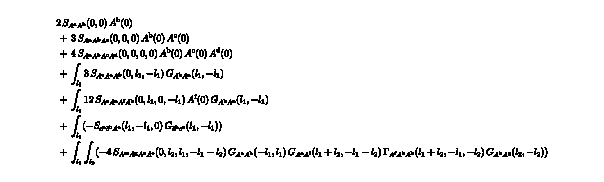

```mathematica
MakeDSE[A[x]]//.{c[_]:>0,cb[_]:>0}//Truncate//FSimplify//Route//FPrint
```

```mathematica
%//FPrint
```

```mathematica
Get["FunKit`"];
fields= <|
"cField"-> {
A[p,{v, c}]
},
"Grassmann"->{
{cb[p,{c}],c[p,{c}]}
}
|>;
truncation=<|
GammaN->{
{A,A},{A,A,A},{A,A,A,A},
{A,cb,c}
},
Propagator->{
{A,A},{cb,c}
},
Rdot->{
{A,A},{cb,c}
},
S->{
{A,A},{A,A,A},{A,A,A,A},
{cb,c},{cb,c,A}
}
|>;
SetTexStyles[cb->"\\bar{c}"];
diagramStyling=<|
"Vertices"->{GammaN,S},
"Edges"->{Propagator},
"Styles"->{A->Orange,c->{Dashed,Black}}
|>;
Setup:=<|
"MasterEquation"->masterEquation,
"FieldSpace"->fields,
"Truncation"->truncation,
"DiagramStyling"->diagramStyling
|>;
SetGlobalSetup[Setup];
```

Loading modules...

...TensorBases loaded

...FEDeriK loaded

...AnSEL loaded

...DiANE loaded

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 1.0
Year: 2025
For more information, call FunKitInfo[].

Loading modules...

...TensorBases loaded

...FEDeriK loaded

...AnSEL loaded

...DiANE loaded

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 1.0
Year: 2025
For more information, call FunKitInfo[].

...DiANE loaded

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 1.0
Year: 2025
For more information, call FunKitInfo[].

```mathematica
DerivativeListAcbc={ A[i1],cb[i2],c[i3]};
TakeDerivatives[Setup,WetterichEquation,DerivativeListAcbc];
%//Truncate//FPrint
```